## Prueba 1

## Cálculos nuevos

### Ecuación 12

```mathematica
A1=a^2
```

0.5

```mathematica
B1=- 2 a Sin[ϕ-γ] Sin[β/2]Sin[α]
```

0.409379

```mathematica
C1=a^2 Cos[α]^2+2a Cos[ϕ-γ] Sin[β/2]Cos[α]Sin[α]+Sin[β/2]^2 Sin[α]^2
```

0.379577

```mathematica
θ1Plus=ArcCos[-(A1+C1-1)/Sqrt[(A1-C1)^2+(B1)^2]]+ArcTan[B1/(A1-C1)]
```

2.56941

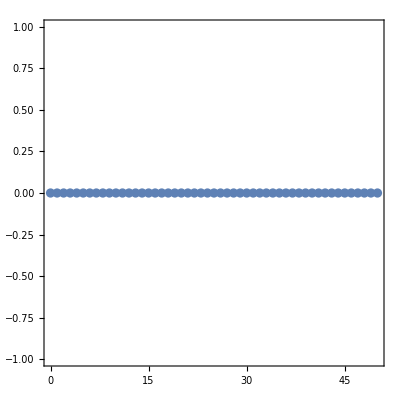

```mathematica
coin0={a,b};
θ=θ1Plus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

```mathematica
θ1Minus=ArcCos[-(A1+C1-1)/(-Sqrt[(A1-C1)^2+(B1)^2])]+ArcTan[B1/(A1-C1)]
```

3.14159

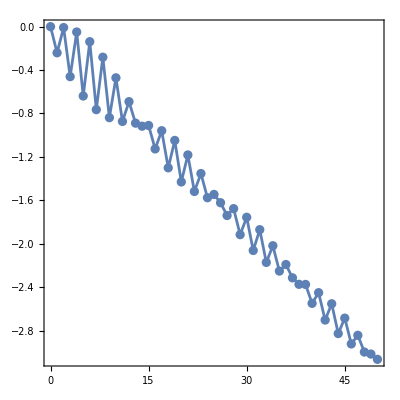

```mathematica
coin0={a,b};
θ=θ1Minus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

### Ecuación 14

```mathematica
A2=Sin[β/2]^2
```

0.5

```mathematica
B2=- 2 a Sin[ϕ-γ] Sin[β/2]Sin[α]
```

0.409379

```mathematica
C2=Sin[β/2]^2 Cos[α]^2-2a Cos[ϕ-γ] Sin[β/2]Cos[α]Sin[α]+a^2 Sin[α]^2
```

0.620423

```mathematica
θ2Plus=ArcCos[-(A2+C2-1)/Sqrt[(A2-C2)^2+(B2)^2]]+ArcTan[B2/(A2-C2)]
```

0.572183

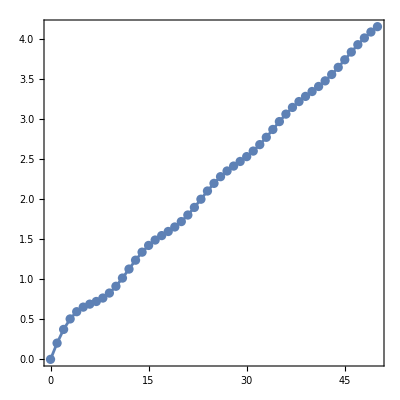

```mathematica
coin0={a,b};
θ=θ2Plus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

```mathematica
θ2Minus=ArcCos[-(A2+C2-1)/(-Sqrt[(A2-C2)^2+(B2)^2])]+ArcTan[B2/(A2-C2)]
```

6.66134×10^-16

```mathematica
coin0={a,b};
θ=θ2Minus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

## Cálculos viejos

### Ecuación 12

```mathematica
A3=Norm[a]^2
```

0.5

```mathematica
B3= 2Im[Exp[ⅈ ϕ]a Conjugate[b]]Sin[α]
```

-0.409379

```mathematica
C3=Norm[a Cos[α]+Exp[-ⅈ ϕ]b Sin[α]]^2
```

0.379577

```mathematica
θ3Plus=ArcCos[-(A3+C3-1)/Sqrt[(A3-C3)^2+(B3)^2]]+ArcTan[B3/(A3-C3)]
```

4.44089×10^-16

```mathematica
coin0={a,b};
θ=θ3Plus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

```mathematica
θ3Minus=ArcCos[-(A3+C3-1)/(-Sqrt[(A3-C3)^2+(B3)^2])]+ArcTan[B3/(A3-C3)]
```

0.572183

```mathematica
coin0={a,b};
θ=θ3Minus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

### Ecuación 14

```mathematica
A4=Norm[b]^2
```

0.5

```mathematica
B4= 2Im[Exp[ⅈ ϕ]a Conjugate[b]]Sin[α]
```

-0.409379

```mathematica
C4=Norm[b Cos[α]-Exp[ⅈ ϕ]a Sin[α]]^2
```

0.620423

```mathematica
θ4Plus=ArcCos[-(A4+C4-1)/Sqrt[(A4-C4)^2+(B4)^2]]+ArcTan[B4/(A4-C4)]
```

3.14159

```mathematica
coin0={a,b};
θ=θ4Plus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

```mathematica
θ4Minus=ArcCos[-(A4+C4-1)/(-Sqrt[(A4-C4)^2+(B4)^2])]+ArcTan[B4/(A4-C4)]
```

2.56941

```mathematica
coin0={a,b};
θ=θ4Minus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

## Prueba 2

```mathematica
{α,ϕ}=RandomQubitState[67,Automatic,Automatic][[;;2]]
```

{2.73212,1.83464}

## Cálculos nuevos

### Ecuación 12

```mathematica
A1=a^2
```

0.5

```mathematica
B1=- 2 a Sin[ϕ-γ] Sin[β/2]Sin[α]
```

-0.397297

```mathematica
C1=a^2 Cos[α]^2+2a Cos[ϕ-γ] Sin[β/2]Cos[α]Sin[α]+Sin[β/2]^2 Sin[α]^2
```

0.523522

```mathematica
θ1Plus=ArcCos[-(A1+C1-1)/Sqrt[(A1-C1)^2+(B1)^2]]+ArcTan[B1/(A1-C1)]
```

3.14159

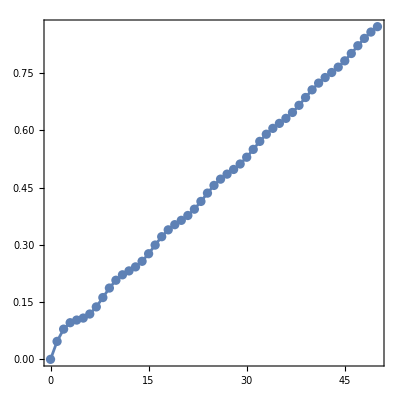

```mathematica
coin0={a,b};
θ=θ1Plus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

```mathematica
θ1Minus=ArcCos[-(A1+C1-1)/(-Sqrt[(A1-C1)^2+(B1)^2])]+ArcTan[B1/(A1-C1)]
```

3.02332

```mathematica
coin0={a,b};
θ=θ1Minus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

### Ecuación 14

```mathematica
A2=Sin[β/2]^2
```

0.5

```mathematica
B2=- 2 a Sin[ϕ-γ] Sin[β/2]Sin[α]
```

-0.397297

```mathematica
C2=Sin[β/2]^2 Cos[α]^2-2a Cos[ϕ-γ] Sin[β/2]Cos[α]Sin[α]+a^2 Sin[α]^2
```

0.476478

```mathematica
θ2Plus=ArcCos[-(A2+C2-1)/Sqrt[(A2-C2)^2+(B2)^2]]+ArcTan[B2/(A2-C2)]
```

-6.66134×10^-16

```mathematica
coin0={a,b};
θ=θ2Plus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

```mathematica
θ2Minus=ArcCos[-(A2+C2-1)/(-Sqrt[(A2-C2)^2+(B2)^2])]+ArcTan[B2/(A2-C2)]
```

0.118273

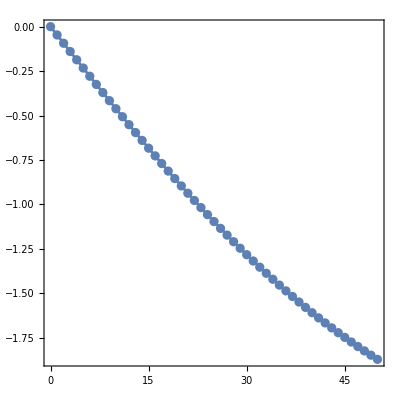

```mathematica
coin0={a,b};
θ=θ2Minus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

## Cálculos viejos

### Ecuación 12

```mathematica
A3=Norm[a]^2
```

0.5

```mathematica
B3= 2Im[Exp[ⅈ ϕ]a Conjugate[b]]Sin[α]
```

0.397297

```mathematica
C3=Norm[a Cos[α]+Exp[-ⅈ ϕ]b Sin[α]]^2
```

0.523522

```mathematica
θ3Plus=ArcCos[-(A3+C3-1)/Sqrt[(A3-C3)^2+(B3)^2]]+ArcTan[B3/(A3-C3)]
```

0.118273

```mathematica
coin0={a,b};
θ=θ3Plus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

```mathematica
θ3Minus=ArcCos[-(A3+C3-1)/(-Sqrt[(A3-C3)^2+(B3)^2])]+ArcTan[B3/(A3-C3)]
```

-4.44089×10^-16

```mathematica
coin0={a,b};
θ=θ3Minus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

### Ecuación 14

```mathematica
A4=Norm[b]^2
```

0.5

```mathematica
B4= 2Im[Exp[ⅈ ϕ]a Conjugate[b]]Sin[α]
```

0.397297

```mathematica
C4=Norm[b Cos[α]-Exp[ⅈ ϕ]a Sin[α]]^2
```

0.476478

```mathematica
θ4Plus=ArcCos[-(A4+C4-1)/Sqrt[(A4-C4)^2+(B4)^2]]+ArcTan[B4/(A4-C4)]
```

3.02332

```mathematica
coin0={a,b};
θ=θ4Plus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

```mathematica
θ4Minus=ArcCos[-(A4+C4-1)/(-Sqrt[(A4-C4)^2+(B4)^2])]+ArcTan[B4/(A4-C4)]
```

3.14159

```mathematica
coin0={a,b};
θ=θ4Minus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

## Prueba 3

```mathematica
{a,b}=RandomQubitState[706,π/2.,3π/4.][[3;;]]
```

{0.707107,-0.5+0.5 ⅈ}

```mathematica
{β,γ}=RandomQubitState[706,π/2.,3π/4.][[;;2]]
```

{1.5708,2.35619}

```mathematica
{α,ϕ}={π/4.,π/4.}
```

{0.785398,0.785398}

## Cálculos nuevos

### Ecuación 12

```mathematica
A1=a^2
```

0.5

```mathematica
B1=- 2 a Sin[ϕ-γ] Sin[β/2]Sin[α]
```

0.707107

```mathematica
C1=a^2 Cos[α]^2+2a Cos[ϕ-γ] Sin[β/2]Cos[α]Sin[α]+Sin[β/2]^2 Sin[α]^2
```

0.5

```mathematica
θ1Plus=ArcCos[-(A1+C1-1)/Sqrt[(A1-C1)^2+(B1)^2]]+ArcTan[B1/(A1-C1)]
```

3.14159

```mathematica
coin0={a,b};
θ=θ1Plus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

```mathematica
θ1Minus=ArcCos[-(A1+C1-1)/(-Sqrt[(A1-C1)^2+(B1)^2])]+ArcTan[B1/(A1-C1)]
```

3.14159

```mathematica
coin0={a,b};
θ=θ1Minus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

### Ecuación 14

```mathematica
A2=Sin[β/2]^2
```

0.5

```mathematica
B2=- 2 a Sin[ϕ-γ] Sin[β/2]Sin[α]
```

0.707107

```mathematica
C2=Sin[β/2]^2 Cos[α]^2-2a Cos[ϕ-γ] Sin[β/2]Cos[α]Sin[α]+a^2 Sin[α]^2
```

0.5

```mathematica
θ2Plus=ArcCos[-(A2+C2-1)/Sqrt[(A2-C2)^2+(B2)^2]]+ArcTan[B2/(A2-C2)]
```

0.

```mathematica
coin0={a,b};
θ=θ2Plus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

```mathematica
θ2Minus=ArcCos[-(A2+C2-1)/(-Sqrt[(A2-C2)^2+(B2)^2])]+ArcTan[B2/(A2-C2)]
```

0.

```mathematica
coin0={a,b};
θ=θ2Minus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

## Prueba 4

```mathematica
{a,b}=RandomQubitState[706,π/2.,Automatic][[3;;]]
```

{0.707107,0.693097+0.140061 ⅈ}

```mathematica
{β,γ}=RandomQubitState[706,π/2.,Automatic][[;;2]]
```

{1.5708,0.199394}

```mathematica
{α,ϕ}={3π/4.,5π/4.}
```

{2.35619,3.92699}

## Cálculos nuevos

### P(1)=1/2

```mathematica
A1=a^2
```

0.5

```mathematica
B1=- 2 a Sin[ϕ-γ] Sin[β/2]Sin[α]
```

0.391056

```mathematica
C1=a^2 Cos[α]^2+2a Cos[ϕ-γ] Sin[β/2]Cos[α]Sin[α]+Sin[β/2]^2 Sin[α]^2
```

0.916579

```mathematica
θ1Plus=ArcCos[-(A1+C1-1)/Sqrt[(A1-C1)^2+(B1)^2]]+ArcTan[B1/(A1-C1)]
```

1.63398

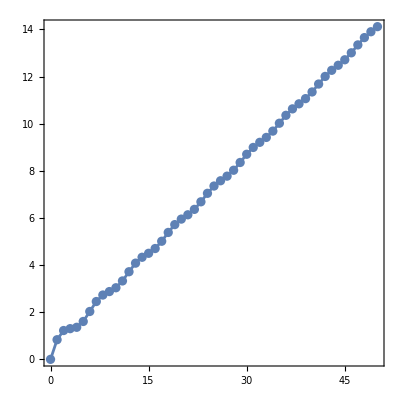

```mathematica
coin0={a,b};
θ=θ1Plus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

```mathematica
θ1Minus=ArcCos[-(A1+C1-1)/(-Sqrt[(A1-C1)^2+(B1)^2])]+ArcTan[B1/(A1-C1)]
```

-6.66134×10^-16

```mathematica
coin0={a,b};
θ=θ1Minus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

-Graphics-

### P(-1)=1/2

```mathematica
A2=Sin[β/2]^2
```

0.5

```mathematica
B2=- 2 a Sin[ϕ-γ] Sin[β/2]Sin[α]
```

0.391056

```mathematica
C2=Sin[β/2]^2 Cos[α]^2-2a Cos[ϕ-γ] Sin[β/2]Cos[α]Sin[α]+a^2 Sin[α]^2
```

0.0834213

```mathematica
θ2Plus=ArcCos[-(A2+C2-1)/Sqrt[(A2-C2)^2+(B2)^2]]+ArcTan[B2/(A2-C2)]
```

1.50761

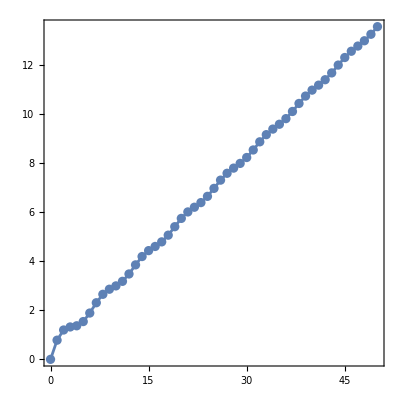

```mathematica
coin0={a,b};
θ=θ2Plus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```

```mathematica
θ2Minus=ArcCos[-(A2+C2-1)/(-Sqrt[(A2-C2)^2+(B2)^2])]+ArcTan[B2/(A2-C2)]
```

3.14159

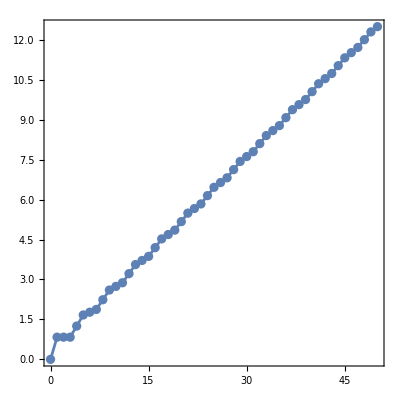

```mathematica
coin0={a,b};
θ=θ2Minus;
t=50;
R=CalculateData[coin0,θ,α,ϕ,t];
ExpValVsTimePlot[R[[2]],t]
```